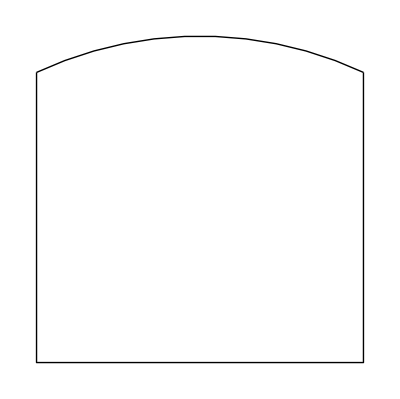

```mathematica
Wt=4.5;(*Largura do Túnel em m*)
Ht=4; (*Altura das Paredes do Túnel em m*)
At=0.5; (*Altura do Arco em m*)

R=(Wt^2+4At^2)/(8At);
Θ=ArcSin[Wt/(2R)];
Tunel = Graphics[{{Line[{{0,Ht},{0,0},{Wt,0},{Wt,Ht}}]}, {Circle[{Wt/2,Ht-R+At},R,{Pi/2-Θ,Pi/2+Θ}]}}];
Show[Tunel]
```